# Контролна работа №2 IV вариант, задача 2 Фак. №2001261051

## Дадена е началната задача за ОДУ: y’ = sin(x^2) + y, y(0) = b, x ϵ [0, 0.4]

### a) Да се намери точното решение на задачата

Търсим точно решение :

```mathematica
Clear[x,y]
DSolve[{y'[x]==Sin[x^2]+y[x], y[0]==1}, y[x],x]
```

{{y[x]→1/4 ⅇ^(-ⅈ/4+x) (4 ⅇ^(ⅈ/4)+(-1)^(3/4) √π Erfi[1/2 (-1)^(1/4)]+(-1)^(1/4) ⅇ^(ⅈ/2) √π Erfi[1/2 (-1)^(3/4)]-(-1)^(3/4) √π Erfi[1/2 (-1)^(3/4) (-ⅈ+2 x)]-(-1)^(1/4) ⅇ^(ⅈ/2) √π Erfi[1/2 (-1)^(1/4) (ⅈ+2 x)])}}

Визуализация на точно решение:

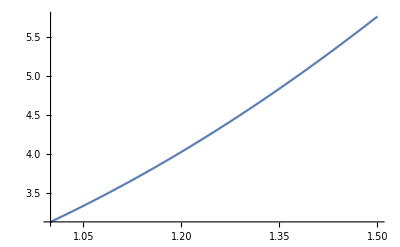

```mathematica
yt[x_]:=1/4 ⅇ^(-ⅈ/4+x) (4 ⅇ^(ⅈ/4)+(-1)^(3/4) √π Erfi[1/2 (-1)^(1/4)]+(-1)^(1/4) ⅇ^(ⅈ/2) √π Erfi[1/2 (-1)^(3/4)]-(-1)^(3/4) √π Erfi[1/2 (-1)^(3/4) (-ⅈ+2 x)]-(-1)^(1/4) ⅇ^(ⅈ/2) √π Erfi[1/2 (-1)^(1/4) (ⅈ+2 x)])
Plot[yt[x], {x, a,b}]
```

### б) По метода на Ойлер да се реши приближено задачата за n = 4. Запишете резултатите в таблица. Сравнете с точното решение

Мрежата е с n = 4 и стъпка h = 0.1

Теоретичната локална грешка  е 0.01

Теоретичната глобална грешка е 0.1

i = 0, x_i = 0., y_i = 1., f_i = 1., y_точно = 1.-5.55112×10^-17 ⅈ, истинска грешка = 5.55112×10^-17

i = 1, x_i = 0.1, y_i = 1.1, f_i = 1.11, y_точно = 1.10551-1.11022×10^-16 ⅈ, истинска грешка = 0.00551275

i = 2, x_i = 0.2, y_i = 1.211, f_i = 1.25099, y_точно = 1.22421-5.55112×10^-17 ⅈ, истинска грешка = 0.013208

i = 3, x_i = 0.3, y_i = 1.3361, f_i = 1.42598, y_точно = 1.35957+0. ⅈ, истинска грешка = 0.0234721

i = 4, x_i = 0.4, y_i = 1.4787, f_i = 1.63801, y_точно = 1.51543+0. ⅈ, истинска грешка = 0.0367364

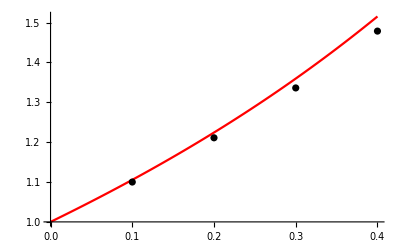

```mathematica
(*Въвеждаме условието на задачата*)
a = 0.;b=0.4;
x = a;
y = 1.;
f[x_,y_] := Sin[x^2]+y

(*Точно решение*)
yt[x_]:=1/4 ⅇ^(-ⅈ/4+x) (4 ⅇ^(ⅈ/4)+(-1)^(3/4) √π Erfi[1/2 (-1)^(1/4)]+(-1)^(1/4) ⅇ^(ⅈ/2) √π Erfi[1/2 (-1)^(3/4)]-(-1)^(3/4) √π Erfi[1/2 (-1)^(3/4) (-ⅈ+2 x)]-(-1)^(1/4) ⅇ^(ⅈ/2) √π Erfi[1/2 (-1)^(1/4) (ⅈ+2 x)])

(*Съставяме мрежата*)
n = 4; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
Print["i = ", i, ", x_i = ", x, ", y_i = ", y, ", f_i = ", f[x,y] , ", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x,y];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

### в) Каква е теоретичната точност на полученото приближено решение?

Отг: последната итерация, което се пада y_точно=1.51543 + 0. i

### г) Каква би била точността при изпозлване на модифицирания метод на Ойлер за поставената задача със същата стъпка? Направете сравнение между двата метода

Мрежата е с n = 4 и стъпка h = 0.1

Теоретичната локална грешка  е 0.001

Теоретичната глобална грешка е 0.01

i = 0, x_i = 0., y_i = 1., f_i = 1., x_(i + 1/2) = 0.05, y_(i + 1/2) = 1.05, f_(i + 1/2) = 1.0525 , y_точно = 1.-5.55112×10^-17 ⅈ, истинска грешка = 5.55112×10^-17

i = 1, x_i = 0.1, y_i = 1.10525, f_i = 1.11525, x_(i + 1/2) = 0.15, y_(i + 1/2) = 1.16101, f_(i + 1/2) = 1.18351 , y_точно = 1.10551-1.11022×10^-16 ⅈ, истинска грешка = 0.000262752

i = 2, x_i = 0.2, y_i = 1.2236, f_i = 1.26359, x_(i + 1/2) = 0.25, y_(i + 1/2) = 1.28678, f_(i + 1/2) = 1.34924 , y_точно = 1.22421-5.55112×10^-17 ⅈ, истинска грешка = 0.000606903

i = 3, x_i = 0.3, y_i = 1.35853, f_i = 1.4484, x_(i + 1/2) = 0.35, y_(i + 1/2) = 1.43095, f_(i + 1/2) = 1.55314 , y_точно = 1.35957+0. ⅈ, истинска грешка = 0.00104597

i = 4, x_i = 0.4, y_i = 1.51384, f_i = 1.67316, x_(i + 1/2) = 0.45, y_(i + 1/2) = 1.5975, f_(i + 1/2) = 1.79862 , y_точно = 1.51543+0. ⅈ, истинска грешка = 0.00159412

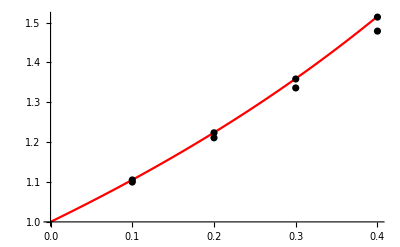

```mathematica
(*Въвеждаме условието на задачата*)
a = 0.;b=0.4;
x = a;
y = 1.;
f[x_,y_] := Sin[x^2]+y

(*Точно решение*)
yt[x_]:=1/4 ⅇ^(-ⅈ/4+x) (4 ⅇ^(ⅈ/4)+(-1)^(3/4) √π Erfi[1/2 (-1)^(1/4)]+(-1)^(1/4) ⅇ^(ⅈ/2) √π Erfi[1/2 (-1)^(3/4)]-(-1)^(3/4) √π Erfi[1/2 (-1)^(3/4) (-ⅈ+2 x)]-(-1)^(1/4) ⅇ^(ⅈ/2) √π Erfi[1/2 (-1)^(1/4) (ⅈ+2 x)])

(*Съставяме мрежата*)
n = 4; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]


(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, ", x_i = ", x, ", y_i = ", y, ", f_i = ", f[x,y]  , ", x_(i + 1/2) = ", x12, ", y_(i + 1/2) = ", y12, ", f_(i + 1/2) = ", f[x12,y12]  ", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]

(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```